# Linearity

```mathematica
theoreticalColor="TropicalRainForest";
experimentalColor="BrickRed";
zeroFreqColor="Razzmatazz";
zeroFreqColorAtF = "ShamRock";
```

ha változtatjuk mu-t, hogyan változik ahhoz képest a C réteg

skewness, szórás check, 0.5 eset?

## Observation

```mathematica
experimentalList={{0.5,23/1000},{1.67, 78/1000},{2,95/1000 },{3,151/1000 },{6,288/1000},{8,391/1000},{10,469/1000},{11, 559/1000},{12, 602/1000},{13, 637/1000},{14,714/1000},{15,774/1000},{16, 839/1000},{16.7, 893/1000},{17,912/1000},{18,957/1000},{19,989/1000},{20,997/1000}};
```

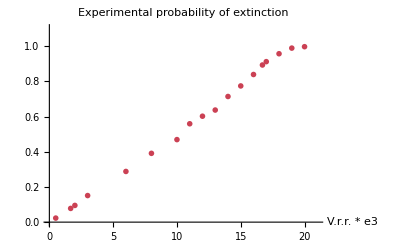

```mathematica
PlotExperimental=ListPlot[experimentalList, 
PlotStyle->{ColorData["Crayola"][experimentalColor],Thickness[0.010]},
PlotMarkers->{{●,10}},PlotRange->{{0,21},{0,1.1}},AxesLabel->{"V.r.r. * e3",""},PlotLabel->"Experimental probability of extinction"]
```

? note: for the majority of the curve above we see ~reasonable linearity, the end seems mollified. Towards the end (vrr = 19, 20) we don’t really have E(X)>>1 (we do have a good geom. fit though),  so the fix point theorem does not hold in itself. (and it is the fix point theorem that gives us linearity at this point)

## Offspring distribution

#### Virus removal rate \in [1.67 , 18] * E-3

```mathematica
VRRString = "13";
VRRNumString="13";
```

```mathematica
data =Import["C:\\Users\\Juhász Nóra\\Documents\\GitHub\\ABM-PDE\\StochasticVariability\\theo_results\\theo"<>VRRString<>".txt", "Table"];
```

```mathematica
dataLength=1000;
```

```mathematica
cleanData={};
```

```mathematica
For[i=1,i<=dataLength, i++,cleanData=Append[cleanData,data[[i]][[4]]]]
```

```mathematica
cleanData
```

{3.,1.,0.,1.,3.,0.,0.,1.,9.,2.,1.,0.,0.,1.,3.,0.,0.,2.,1.,2.,1.,5.,2.,3.,2.,6.,1.,1.,1.,0.,4.,4.,1.,0.,1.,0.,2.,0.,1.,0.,0.,0.,4.,7.,0.,0.,1.,0.,0.,0.,2.,0.,2.,0.,1.,3.,1.,5.,3.,0.,2.,1.,0.,2.,1.,0.,0.,1.,1.,5.,2.,4.,0.,0.,2.,0.,0.,1.,2.,2.,5.,6.,2.,0.,0.,0.,2.,1.,0.,6.,5.,1.,0.,1.,0.,0.,0.,1.,1.,0.,2.,3.,3.,3.,6.,4.,1.,0.,4.,1.,1.,1.,0.,3.,0.,1.,1.,1.,3.,0.,4.,1.,4.,0.,1.,2.,0.,1.,3.,0.,0.,0.,4.,10.,0.,0.,3.,2.,0.,4.,1.,1.,0.,2.,0.,3.,1.,1.,1.,2.,2.,3.,0.,1.,2.,2.,2.,0.,0.,0.,0.,2.,4.,1.,1.,0.,1.,1.,1.,0.,3.,0.,1.,2.,4.,2.,2.,4.,0.,0.,1.,0.,1.,0.,1.,0.,0.,5.,2.,3.,0.,4.,2.,1.,0.,0.,2.,0.,2.,6.,2.,1.,0.,1.,1.,5.,0.,1.,1.,0.,2.,1.,0.,3.,0.,1.,0.,3.,0.,3.,0.,0.,0.,4.,2.,0.,0.,1.,3.,1.,0.,3.,0.,2.,1.,1.,0.,7.,3.,0.,1.,1.,0.,0.,1.,0.,0.,0.,5.,1.,5.,4.,0.,1.,0.,2.,1.,3.,0.,5.,0.,0.,2.,0.,0.,0.,0.,1.,5.,0.,1.,9.,1.,1.,0.,0.,0.,1.,0.,1.,0.,1.,0.,1.,1.,0.,1.,1.,1.,0.,2.,1.,1.,4.,1.,0.,1.,1.,2.,2.,0.,3.,1.,4.,2.,2.,0.,0.,0.,1.,0.,4.,2.,0.,1.,2.,0.,3.,5.,2.,0.,0.,3.,2.,0.,0.,0.,8.,0.,2.,3.,0.,1.,1.,0.,1.,0.,1.,3.,0.,0.,1.,0.,2.,0.,0.,0.,0.,3.,5.,2.,3.,1.,1.,1.,5.,3.,2.,1.,0.,0.,2.,0.,7.,4.,1.,1.,0.,0.,3.,3.,3.,2.,0.,1.,3.,3.,1.,0.,0.,0.,3.,3.,2.,0.,0.,2.,1.,8.,1.,1.,2.,1.,0.,0.,3.,0.,2.,4.,1.,1.,1.,3.,0.,0.,0.,0.,2.,3.,1.,2.,2.,0.,0.,0.,0.,0.,3.,2.,2.,2.,10.,1.,0.,6.,1.,1.,3.,3.,0.,1.,1.,0.,0.,7.,0.,2.,0.,3.,0.,0.,2.,6.,1.,0.,1.,0.,2.,0.,0.,0.,0.,1.,0.,0.,1.,0.,3.,0.,4.,9.,1.,0.,1.,2.,1.,0.,0.,1.,1.,3.,6.,2.,5.,2.,0.,0.,8.,2.,3.,1.,1.,0.,1.,0.,3.,1.,0.,2.,3.,1.,1.,3.,0.,3.,2.,1.,0.,3.,0.,4.,1.,0.,3.,2.,3.,2.,3.,1.,2.,0.,5.,0.,0.,2.,2.,0.,0.,0.,0.,3.,0.,0.,0.,4.,0.,0.,1.,4.,2.,1.,2.,2.,1.,3.,0.,1.,0.,3.,0.,3.,2.,2.,2.,0.,1.,0.,3.,1.,0.,1.,3.,4.,1.,1.,0.,3.,2.,0.,2.,1.,8.,1.,1.,0.,3.,1.,0.,0.,5.,6.,0.,0.,0.,0.,0.,0.,2.,4.,0.,0.,2.,1.,0.,0.,0.,9.,0.,0.,0.,1.,1.,10.,0.,0.,0.,0.,2.,1.,1.,0.,0.,2.,0.,1.,0.,0.,2.,0.,0.,0.,3.,1.,0.,4.,2.,3.,4.,2.,3.,4.,2.,0.,5.,2.,1.,1.,4.,4.,2.,8.,5.,2.,4.,0.,0.,2.,1.,5.,2.,9.,0.,3.,1.,1.,3.,3.,4.,8.,0.,2.,1.,1.,4.,1.,0.,0.,5.,1.,0.,0.,1.,1.,0.,3.,1.,0.,0.,3.,2.,0.,0.,6.,0.,5.,1.,0.,0.,0.,0.,0.,2.,0.,0.,0.,2.,0.,1.,0.,0.,1.,0.,0.,1.,9.,6.,0.,3.,5.,1.,1.,0.,0.,0.,0.,6.,2.,0.,4.,2.,1.,0.,3.,5.,2.,1.,2.,1.,0.,1.,0.,2.,4.,5.,0.,2.,0.,0.,3.,0.,1.,0.,0.,4.,1.,6.,2.,0.,2.,2.,1.,0.,4.,0.,7.,0.,2.,3.,3.,1.,1.,1.,0.,0.,0.,2.,0.,5.,1.,0.,0.,2.,1.,0.,0.,0.,0.,3.,0.,0.,0.,1.,1.,0.,1.,3.,0.,1.,2.,0.,0.,1.,1.,1.,1.,8.,0.,1.,0.,3.,1.,0.,0.,2.,3.,4.,6.,1.,2.,1.,1.,0.,0.,0.,0.,4.,8.,0.,2.,0.,3.,1.,3.,1.,1.,0.,3.,1.,0.,0.,0.,3.,0.,6.,3.,3.,3.,1.,6.,3.,1.,3.,2.,1.,0.,0.,1.,1.,1.,0.,0.,1.,4.,5.,0.,0.,0.,0.,0.,0.,3.,2.,0.,4.,1.,4.,0.,2.,4.,1.,0.,5.,2.,6.,2.,0.,1.,9.,1.,2.,0.,8.,1.,1.,2.,0.,0.,0.,1.,1.,0.,5.,0.,3.,0.,0.,4.,2.,0.,2.,4.,5.,4.,0.,3.,0.,1.,0.,1.,0.,1.,1.,1.,1.,0.,0.,2.,0.,1.,0.,0.,1.,0.,1.,1.,2.,2.,1.,1.,2.,3.,0.,1.,3.,2.,0.,3.,1.,1.,4.,0.,3.,4.,0.,5.,0.,0.,1.,2.,1.,6.,1.,2.,7.,1.,2.,1.,0.,0.,3.,0.,3.,4.,1.,1.,1.,3.,2.,3.,1.,0.,0.,0.,1.,1.,0.,4.,3.,3.,0.,0.,0.,1.,0.,0.,0.,4.,6.,2.,0.,2.,0.,2.,0.,1.,1.,0.,3.,1.,2.,2.,11.,1.,0.,0.,0.,0.,1.,0.,1.}

```mathematica
probabilityData={};
```

```mathematica
For[i=0,i<=Max[cleanData], i++,probabilityData=Append[probabilityData,{i,0}]]
```

```mathematica
probabilityData
```

{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0}}

```mathematica
For[i=1,i<=dataLength, i++,probabilityData[[cleanData[[i]]+1,2]]=probabilityData[[cleanData[[i]]+1,2]] + 1]
```

```mathematica
probabilityData
```

{{0,376},{1,248},{2,142},{3,105},{4,53},{5,31},{6,19},{7,6},{8,9},{9,7},{10,3},{11,1}}

check if the expected value is > 1 (it is a condition in the fix point theorem)

```mathematica
N[Sum[probabilityData[[i,1]]*probabilityData[[i,2]]/1000,{i,1,Length[probabilityData]}]]
```

1.546

```mathematica
p1=Histogram[cleanData,{0,Max[cleanData],1},"Probability",ChartStyle->"Pastel",PlotLabel->"VRR="<>VRRNumString<>"E-3. Shown against geometric distr., Freq. Zero"];
```

```mathematica
p2=DiscretePlot[PDF[GeometricDistribution[probabilityData[[1,2]]/1000],x]//Evaluate,{x,0,Max[cleanData]},PlotMarkers->Automatic];
```

```mathematica
probabilityData[[1,2]]/1000 //N
```

0.376

```mathematica
Rasterize[Show[p1,p2]]
```

-Graphics-

Gábor ötlete: geom param: mintaátlag reciproka, ML becslés; K-S próba.
Végeredmény: melyik param becslés ad jobb illeszkedést.

```mathematica
geohope=1/(Mean[cleanData]+1)
```

0.392773

```mathematica
Max[cleanData]
```

11.

```mathematica
geohope
```

0.392773

```mathematica
p1=Histogram[cleanData,{0,Max[cleanData],1},"Probability",ChartStyle->"Pastel",PlotLabel->"VRR="<>VRRNumString<>"E-3. Shown against geometric distr., MLE"];
```

```mathematica
p2=DiscretePlot[PDF[GeometricDistribution[geohope],x]//Evaluate,{x,0,Max[cleanData]},PlotMarkers->Automatic];
```

```mathematica
Rasterize[Show[p1,p2]]
```

-Graphics-

```mathematica
KolmogorovSmirnovTest[cleanData,GeometricDistribution[geohope]]
```

KolmogorovSmirnovTest::dscrt: The p-value returned by the KolmogorovSmirnov test may not reflect the true size of the test for discrete test distributions.

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

0.936575

Observation: we seem to have a reasonable fit to geometric distribution, where the distribution’s only parameter is set to the relative frequency of 0 offsprings. This holds for a wide range of VRR values, not just mu=3.

#### Virus removal rate = very small, i.e. 0.5*E-3: in this case it loses the nice geometrical fit

```mathematica
data =Import["C:\\Users\\Juhász Nóra\\Documents\\GitHub\\ABM-PDE\\StochasticVariability\\theo_results\\theo0dot5.txt", "Table"];
```

```mathematica
dataLength=1000;
```

```mathematica
cleanData={};
```

```mathematica
For[i=2,i<=2*dataLength, i=i+2,cleanData=Append[cleanData,data[[i]][[4]]]]
```

```mathematica
filteredData=Select[cleanData, #>1&];
```

```mathematica
Length[filteredData]
```

954

```mathematica
MLE05=1/(3+Mean[filteredData])
```

0.0220334

```mathematica
Sqrt[Variance[cleanData]]
```

42.4137

```mathematica
Sqrt[(1-MLE05)/MLE05/MLE05]
```

44.883

```mathematica
probabilityData={};
```

```mathematica
For[i=0,i<=Max[cleanData], i++,probabilityData=Append[probabilityData,{i,0}]]
```

```mathematica
probabilityData;
```

```mathematica
For[i=1,i<=dataLength, i++,probabilityData[[cleanData[[i]]+1,2]]=probabilityData[[cleanData[[i]]+1,2]] + 1]
```

```mathematica
probabilityData
```

{{0,19},{1,27},{2,35},{3,26},{4,24},{5,21},{6,22},{7,22},{8,18},{9,26},{10,26},{11,9},{12,13},{13,11},{14,15},{15,12},{16,16},{17,18},{18,22},{19,14},{20,19},{21,16},{22,12},{23,12},{24,16},{25,16},{26,8},{27,8},{28,11},{29,12},{30,10},{31,10},{32,13},{33,11},{34,7},{35,8},{36,11},{37,13},{38,7},{39,9},{40,6},{41,11},{42,10},{43,9},{44,9},{45,8},{46,8},{47,7},{48,7},{49,6},{50,13},{51,4},{52,2},{53,6},{54,8},{55,10},{56,1},{57,7},{58,8},{59,12},{60,6},{61,3},{62,6},{63,6},{64,1},{65,7},{66,3},{67,3},{68,3},{69,3},{70,7},{71,4},{72,6},{73,4},{74,3},{75,1},{76,6},{77,2},{78,3},{79,4},{80,4},{81,1},{82,4},{83,1},{84,4},{85,1},{86,3},{87,3},{88,2},{89,1},{90,1},{91,5},{92,1},{93,0},{94,3},{95,3},{96,7},{97,3},{98,3},{99,1},{100,1},{101,1},{102,2},{103,1},{104,5},{105,0},{106,0},{107,2},{108,1},{109,5},{110,1},{111,3},{112,2},{113,2},{114,1},{115,2},{116,5},{117,1},{118,1},{119,2},{120,2},{121,1},{122,2},{123,0},{124,0},{125,0},{126,0},{127,0},{128,0},{129,2},{130,1},{131,0},{132,2},{133,0},{134,1},{135,2},{136,2},{137,1},{138,1},{139,0},{140,3},{141,1},{142,1},{143,0},{144,1},{145,0},{146,0},{147,1},{148,1},{149,0},{150,1},{151,1},{152,0},{153,1},{154,1},{155,0},{156,0},{157,1},{158,0},{159,1},{160,0},{161,0},{162,0},{163,1},{164,0},{165,1},{166,0},{167,0},{168,0},{169,0},{170,0},{171,1},{172,1},{173,2},{174,0},{175,0},{176,0},{177,0},{178,1},{179,0},{180,0},{181,0},{182,0},{183,0},{184,1},{185,0},{186,0},{187,0},{188,0},{189,0},{190,0},{191,0},{192,0},{193,0},{194,1},{195,1},{196,0},{197,1},{198,0},{199,0},{200,0},{201,0},{202,1},{203,0},{204,0},{205,0},{206,0},{207,1},{208,1},{209,1},{210,0},{211,0},{212,0},{213,0},{214,0},{215,0},{216,0},{217,1},{218,0},{219,0},{220,0},{221,1},{222,0},{223,0},{224,1},{225,0},{226,0},{227,0},{228,0},{229,0},{230,0},{231,0},{232,0},{233,0},{234,0},{235,0},{236,0},{237,0},{238,0},{239,0},{240,0},{241,0},{242,0},{243,0},{244,0},{245,1},{246,0},{247,0},{248,0},{249,0},{250,0},{251,0},{252,0},{253,0},{254,0},{255,0},{256,0},{257,0},{258,0},{259,0},{260,0},{261,0},{262,0},{263,0},{264,0},{265,0},{266,1},{267,0},{268,0},{269,0},{270,1},{271,0},{272,0},{273,0},{274,0},{275,0},{276,0},{277,0},{278,0},{279,0},{280,0},{281,0},{282,0},{283,0},{284,0},{285,0},{286,0},{287,0},{288,0},{289,0},{290,0},{291,0},{292,0},{293,0},{294,0},{295,0},{296,0},{297,0},{298,0},{299,0},{300,0},{301,0},{302,0},{303,0},{304,0},{305,0},{306,0},{307,0},{308,0},{309,0},{310,0},{311,0},{312,0},{313,0},{314,0},{315,0},{316,0},{317,1}}

check if the expected value is > 1 (it is a condition in the fix point theorem)

```mathematica
N[Sum[probabilityData[[i,1]]*probabilityData[[i,2]]/1000,{i,1,Length[probabilityData]}]]
```

40.463

```mathematica
p1=Histogram[cleanData,{0,Max[cleanData],1},"Probability",ChartLegends->{"Offspring histogram, VRR=3*E-3."},ChartStyle->"Pastel",PlotLabel->"Shown against geometric distr."];
```

```mathematica
p2=DiscretePlot[PDF[GeometricDistribution[probabilityData[[1,2]]/1000],x]//Evaluate,{x,0,Max[cleanData]},PlotMarkers->Automatic];
```

```mathematica
Rasterize[Show[p1,p2]]
```

-Graphics-

```mathematica
geohope=1/(Mean[cleanData]+1)
```

0.0241179

```mathematica
p2=DiscretePlot[PDF[GeometricDistribution[geohope],x]//Evaluate,{x,0,Max[cleanData]},PlotMarkers->Automatic];
```

```mathematica
Rasterize[Show[p1,p2]]
```

-Graphics-

```mathematica
KolmogorovSmirnovTest[cleanData,GeometricDistribution[geohope]]
```

KolmogorovSmirnovTest::dscrt: The p-value returned by the KolmogorovSmirnov test may not reflect the true size of the test for discrete test distributions.

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

0.304284

Observation: we seem to have a reasonable fit to geometric distribution, where the distribution’s only parameter is set to the relative frequency of 0 offsprings. This holds for a wide range of VRR values, not just mu=3.

## Original idea: The relative frequency of 0. [obsolete]

For each virus removal rate value we run a series of experiments and calculate the relative frequency of 0 offsprings.

```mathematica
vrrrangemax=19;
```

```mathematica
theoFreqZeroList={{0.5,19/1000},{2.0,89/1000},{3,114/1000},{4,191/1000},{5,189/1000},{6,212/1000},{8,270/1000},{13,376/1000},{15,421/1000},{16.7, 460/1000},{18,466/1000}};
```

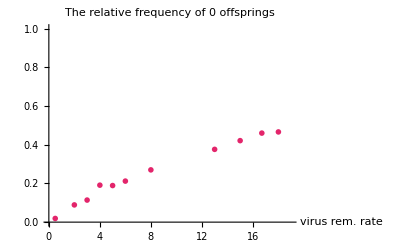

```mathematica
PlotZeroFreq=ListPlot[theoFreqZeroList, 
PlotStyle->{ColorData["Crayola"][zeroFreqColor],Thickness[0.010]},
PlotMarkers->{{●,10}},
PlotRange->{{0,vrrrangemax},{0,1}},AxesLabel->{"virus rem. rate",""},PlotLabel->"The relative frequency of 0 offsprings"]
```

This looks similar to part of the 1/(1+(a/x)^n) curve -- Hill equation with n=1:

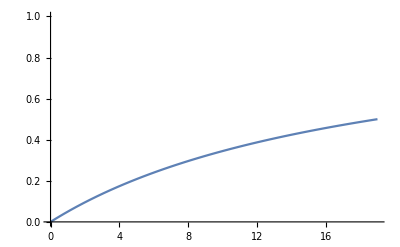

```mathematica
curvePlot=Plot[1/(1+(vrrrangemax/x)),{x,0,vrrrangemax},PlotRange->{0,1}]
```

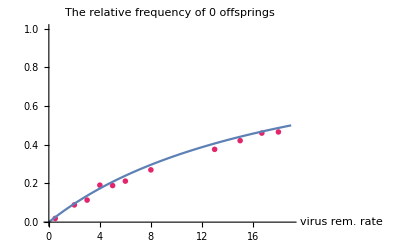

```mathematica
Show[PlotZeroFreq,curvePlot]
```

## The Maximum Likelihood estimate of the parameter of the geometric distribution.

For each virus removal rate value we run a series of experiments and calculate the relative frequency of 0 offsprings.

```mathematica
vrrrangemax=20;
```

```mathematica
MLEstList={{1.67,0.07431},{2.0,0.091424},{3,0.128617},{4,0.167476},{5,0.1970055},{6,0.219202104340201},{8,0.27708506},{13,0.392772},{15,0.443852},{16.7, 0.468603},{18,0.47664}};
```

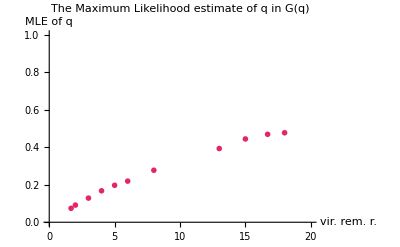

```mathematica
PlotZeroFreq=ListPlot[MLEstList, 
PlotStyle->{ColorData["Crayola"][zeroFreqColor],Thickness[0.010]},
PlotMarkers->{{●,10}},
PlotRange->{{0,vrrrangemax},{0,1}},AxesLabel->{"vir. rem. r.","MLE of q"},PlotLabel->"The Maximum Likelihood estimate of q in G(q)"]
```

This looks similar to part of the 1/(1+(a/x)^n) curve -- Hill equation with n=1:

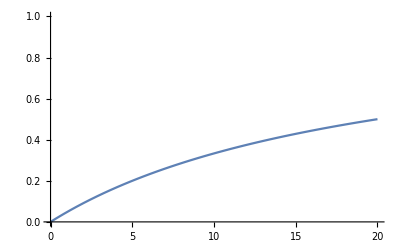

```mathematica
curvePlot=Plot[1/(1+(vrrrangemax/x)),{x,0,vrrrangemax},PlotRange->{0,1}]
```

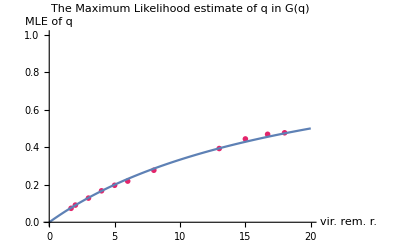

```mathematica
Show[PlotZeroFreq,curvePlot]
```

Observation nr2: at this point we have a concave function.

## Branching processes: the theoretical PoE

Using the above observation regarding a reasonable fit to geometrical distribution, the PoE is given by the fix point of the PGF of the geometrical distribution.

The POE is given by

G_X(q)=q
q / (1 - (1-q)x) = x, thus we have
q = x * (1 - (1-q)x) 

We have a simple second order equation. The non-negative solution to that is:

```mathematica
Rasterize[Plot[N[(1-Sqrt[1-4*(1-(q))*(q)])/(2*(1-(q)))],{q,0,1},PlotLabel->"The G_X(q)=q fixpoint eq.'s solution for geom. distr.",AxesLabel->{"q","PoE"}]]
```

-Graphics-

We have seen that q = q(mu), where we found that q = q(mu) takes the following form: q(mu) = 1 / (1 + 20/mu)

Altogether we have

q / (1 - (1-q)x) = x and
q(mu) = 1 / (1 + 20/mu)

The probability of extinction is given (below on the LHS) as a function of q (the relative frequency of 0 offsprings), and for that to be a linear function of mu we need the following:

```mathematica
Solve[(1-Sqrt[1-4*(1-q)*q])/(2*(1-q))==(1/20)*mu,q]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{q→mu/(20+mu)}}

Which corresponds to what we have previously observed.

## Theoretical linearity

```mathematica
PoE[q_]:=(1-Sqrt[1-4*(1-q)*q])/(2*(1-q))
```

```mathematica
qMLE[mu_]:=1/(1 + 19/mu)
```

```mathematica
POEqMLE={{0.5,PoE[qMLE[0.5]]},{2.0,PoE[qMLE[2.0]]},{3,PoE[qMLE[3.0]]},{4,PoE[qMLE[4.0]]},{5,PoE[qMLE[5]]},{6,PoE[qMLE[6]]},{8,PoE[qMLE[8]]},{10,PoE[qMLE[10]]},{13,PoE[qMLE[13]]},{15,PoE[qMLE[15]]},{16.7, PoE[qMLE[16.7]]},{18,PoE[qMLE[18]]},{19,PoE[qMLE[19]]},{20,PoE[qMLE[20]]}};
```

```mathematica
experimentalList={{0.5,23/1000},{1.67, 78/1000},{2,95/1000 },{6,288/1000},{8,391/1000},{10,469/1000},{11, 559/1000},{12, 602/1000},{13, 637/1000},{14,714/1000},{15,774/1000},{16, 839/1000},{16.7, 893/1000},{17,912/1000},{18,957/1000},{19,989/1000},{20,997/1000}};
```

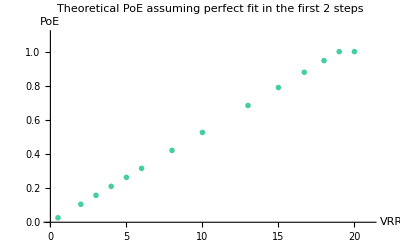

```mathematica
PlotZeroFreqAtF=ListPlot[{POEqMLE}, 
PlotStyle->{{ColorData["Crayola"]["ShamRock"],Thickness[0.010]},{ColorData["Crayola"]["BrickRed"],Thickness[0.010]}},
PlotMarkers->{{●,10}},
PlotRange->{{0,21},{0,1.1}},AxesLabel->{"VRR","PoE"},PlotLabel->"Theoretical PoE assuming perfect fit in the first 2 steps"]
```

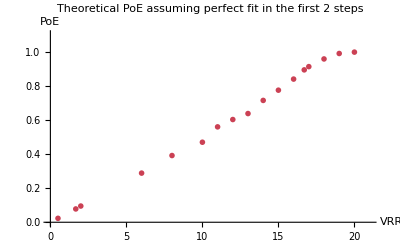

```mathematica
PlotZeroFreqAtF=ListPlot[{experimentalList}, 
PlotStyle->{ColorData["Crayola"]["BrickRed"],Thickness[0.010]},
PlotMarkers->{{●,10}},
PlotRange->{{0,21},{0,1.1}},AxesLabel->{"VRR","PoE"},PlotLabel->"Theoretical PoE assuming perfect fit in the first 2 steps"]
```

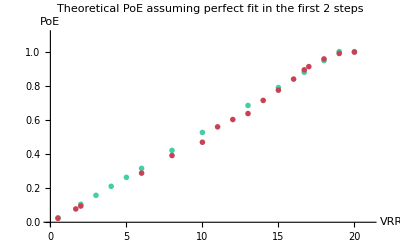

```mathematica
PlotZeroFreqAtF=ListPlot[{POEqMLE,experimentalList}, 
PlotStyle->{{ColorData["Crayola"]["ShamRock"],Thickness[0.010]},{ColorData["Crayola"]["BrickRed"],Thickness[0.010]}},
PlotMarkers->{{●,10}},
PlotRange->{{0,21},{0,1.1}},AxesLabel->{"VRR","PoE"},PlotLabel->"Elméleti vs. tapasztalati kihalási valószínűség"]
```

#### Virus removal rate \in [1.67 , 18] * E-3

```mathematica
VRRString = "4";
VRRNumString="4";
```

```mathematica
data =Import["C:\\Users\\Juhász Nóra\\Documents\\GitHub\\ABM-PDE\\StochasticVariability\\doubleinittheoresults\\vrr"<>VRRString<>".txt", "Table"];
```

```mathematica
dataLength=1000;
```

```mathematica
cleanData={};
```

```mathematica
For[i=1,i<=dataLength, i++,cleanData=Append[cleanData,data[[i]][[4]]]]
```

```mathematica
cleanData;
```

```mathematica
probabilityData={};
```

```mathematica
For[i=0,i<=Max[cleanData], i++,probabilityData=Append[probabilityData,{i,0}]]
```

```mathematica
probabilityData
```

{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},{16,0},{17,0},{18,0},{19,0},{20,0},{21,0},{22,0},{23,0},{24,0},{25,0},{26,0},{27,0},{28,0},{29,0},{30,0},{31,0},{32,0},{33,0},{34,0},{35,0},{36,0},{37,0},{38,0},{39,0},{40,0},{41,0},{42,0},{43,0},{44,0},{45,0},{46,0},{47,0},{48,0},{49,0},{50,0},{51,0},{52,0},{53,0},{54,0},{55,0}}

```mathematica
For[i=1,i<=dataLength, i++,probabilityData[[cleanData[[i]]+1,2]]=probabilityData[[cleanData[[i]]+1,2]] + 1]
```

```mathematica
probabilityData
```

{{0,23},{1,38},{2,53},{3,85},{4,59},{5,65},{6,63},{7,71},{8,67},{9,52},{10,42},{11,43},{12,44},{13,30},{14,29},{15,35},{16,26},{17,23},{18,19},{19,21},{20,15},{21,12},{22,7},{23,13},{24,5},{25,11},{26,9},{27,4},{28,2},{29,4},{30,8},{31,4},{32,1},{33,3},{34,1},{35,2},{36,0},{37,2},{38,2},{39,0},{40,0},{41,1},{42,0},{43,0},{44,0},{45,1},{46,1},{47,2},{48,1},{49,0},{50,0},{51,0},{52,0},{53,0},{54,0},{55,1}}

check if the expected value is > 1 (it is a condition in the fix point theorem)

```mathematica
N[Sum[probabilityData[[i,1]]*probabilityData[[i,2]]/1000,{i,1,Length[probabilityData]}]]
```

10.121

```mathematica
p1=Histogram[cleanData,{0,Max[cleanData],1},"Probability",ChartStyle->"Pastel",PlotLabel->"VRR="<>VRRNumString<>"E-3. Shown against geometric distr., Freq. Zero"];
```

```mathematica
p2=DiscretePlot[PDF[NegativeBinomialDistribution[2,0.16747613465081226],x]//Evaluate,{x,0,Max[cleanData]},PlotMarkers->Automatic];
```

```mathematica
probabilityData[[1,2]]/1000 //N
```

0.023

```mathematica
Rasterize[Show[p1,p2]]
```

-Graphics-

```mathematica
KolmogorovSmirnovTest[cleanData,NegativeBinomialDistribution[2,0.16747613465081226]]
```

KolmogorovSmirnovTest::dscrt: The p-value returned by the KolmogorovSmirnov test may not reflect the true size of the test for discrete test distributions.

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

0.853209

```mathematica
KolmogorovSmirnovTest[cleanData,NegativeBinomialDistribution[2,0.16747613465081226],"TestDataTable"]
```

KolmogorovSmirnovTest::dscrt: The p-value returned by the KolmogorovSmirnov test may not reflect the true size of the test for discrete test distributions.

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

| Statistic | P-Value
Kolmogorov-Smirnov | 0.0190703 | 0.853209

## Stuff

### 1) a végén látható ellapulás

### 2) két fgtlen geometriai összege

### 3) miért G-W

ld.: pdf

a modellünkben, reciprok szerint
sejthalálra plotolva is lineáris lesz az R0 képlet miatt, I-re és beta-ra 1/x szerű lesz.
(miért lesz geometriai?)
lin öf.

más eloszlások is adnak-e lin. öf.-t? (1/E(X)- fgv-ként)
más ágens modell is geom.-t ad-e?

nincs-e olyan univ. dolog h a poe vmi szép fgv.-e Mean(X)-nek.

egyszerűsített esetben kijön-e a geom eloszlás ()
- neg. bin.

p q(1-q)
2p q*q(1-q)
3p q*q*q*(1-q)

V-t fertőz meg
annyiszora djuk össze a V

V + ... + V, Y-szor összeadva, ez geom.-e?

intuíció: miért az,
az h szép fgv-e E(X)-nek az geom.-spec.-e,

1 param eo : alpha, gen fgv fixpontja

General::munfl: Exp[-1399.89] is too small to represent as a normalized machine number; precision may be lost.

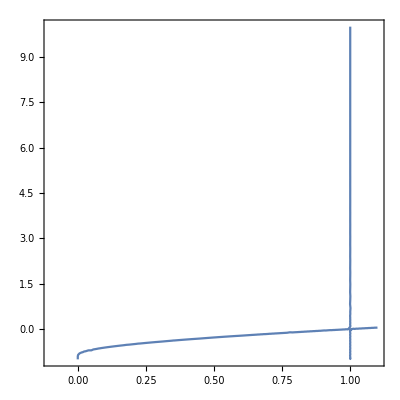

```mathematica
ContourPlot[Exp[(1/(1+(1/(1/lambda))))*(z-1)]==z,{z,-0.1,1.1},{lambda,-1,10}]
```

```mathematica
Exponent
```

Exponent

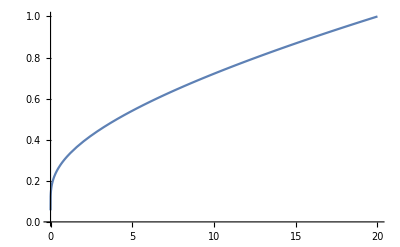

```mathematica
Plot[1/f[u], {u,0,20}]
```

```mathematica
f[u_]:=Log[(u)/n]*n/((u)-n)/. n-> 20
```

```mathematica
f[1]
```

(20 Log[20])/19

```mathematica
N[(20 Log[20])/19]
```

3.1534

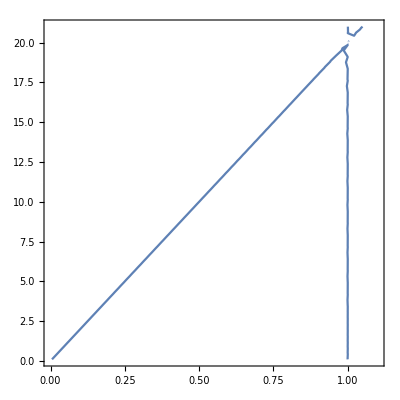

```mathematica
ContourPlot[Exp[f[lambda]*(z-1)]==z,{z,0,1.1},{lambda,0.1,21}]
```

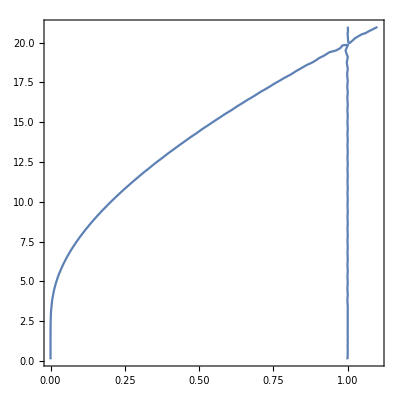

```mathematica
ContourPlot[Exp[20/mu*(z-1)]==z,{z,0,1.1},{mu,0.1,21}]
```

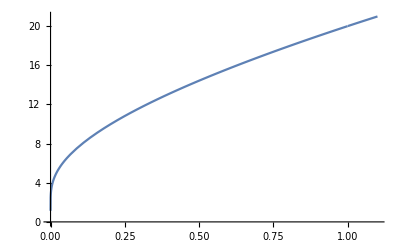

```mathematica
Plot[20*(z-1)/Log[z],{z,0,1.1}]
```

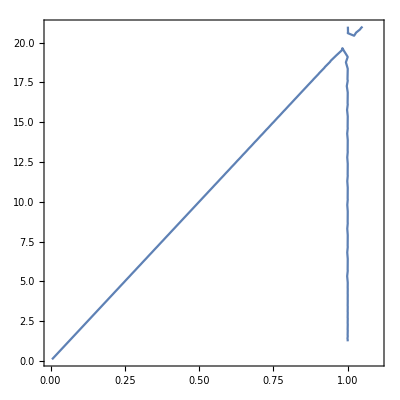

```mathematica
ContourPlot[(1/(1+20/mu))/(1-(1-(1/(1+20/mu)))*z)==z,{z,0,1.1},{mu,0.1,21}]
```